## Pre-Computing the BRDF Integral

We need to find a way to approximate the lighting integral for the specular part of our area light.
The integral writes as:

	L(ω_o)=∫_Ω L(ω_i) f_r(ω_o,ω_i)(ω_i.n)dω_i
	
Ω is the solid angle covered by the upper hemisphere above the surface.

We proceed in the same way as http://blog.selfshadow.com/publications/s2013-shading-course/karis/s2013_pbs_epic _notes _v2.pdf to separate the integral in several parts:

#### Splitting the integral

L(ω_o)≃ ∫_Ω L(ω_i,ρ) (ω_i.n) dω_i  ∫_Ω f_r(ω_o,ω_i)(ω_i.n)dω_i

∫_Ω L'(ω_i,ρ) (ω_i.n) dω_i  represents the pre-filtered source of radiance. It could be an env-map in the case of IBL, or our area light in this case.
∫_Ω f_r(ω_o,ω_i)(ω_i.n)dω_i represents the BRDF integral as if lit by a uniform source of radiance (L(ω_i)=1).

#### BRDF integral

Here, we’ re going to concentrate on the BRDF integral.
Assuming the BRDF f_r(ω_o,ω_i) is our Ward-Dür model, coupled with Fresnel, we obtain:

	L_brdf(ω_o)≃ ∫_Ω  F(ω_o,ω_i,n) D(ω_o,ω_i,n) (ω_i.n)dω_i

F(ω_o,ω_i,n) is the Fresnel term (note that we’ll use the Schlick' s fresnel approximation, not our complex fresnel otherwise the integral would be more difficult to separate).
D(ω_o,ω_i,n) is the Normal Distribution Function of the micro-facet model.
There is no masking/shadowing term as it is already accounted for by the Ward-Dür NDF.

Assuming the Schlick fresnel term is:

	F_schlick(ω_o,h)=F_0+(1-F_0)(1-ω_o.h)^5 = F_0 (1-(1-ω_o.h)^5) + (1-ω_o.h)^5 

We can further split the integral into 2 parts:

	L_brdf(ω_o)≃ F_0∫_Ω  (1-(1-ω_o.h)^5)D(ω_o,ω_i,n) (ω_i.n)dω_i + ∫_Ω  (1-ω_o.h)^5 D(ω_o,ω_i,n) (ω_i.n)dω_i

Ignoring anisotropy, we have:

	D(ω_o,ω_i,n,α) = ρ_s/πα^2 e^(-(tan^2 Θ_h)/α^2) 2(1+cos Θ_l cos Θ_v +sin Θ_l sin Θ_v cos( Φ_v-Φ_l))/(cos Θ_l + cos Θ_v)^4 

Or:
	D(ω_o,ω_i,n,α) = ρ_s/πα^2 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4
	
and ĥ = ω_o +ω_i  (non-normalized!)
	
This gives us:

	L_brdf(ω_o,α)≃ ρ_s/πα^2[ F_0∫_Ω  (1-(1-ω_o.h)^5)e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 (ω_i.n)dω_i + ∫_Ω  (1-ω_o.h)^5 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 (ω_i.n)dω_i]
	
	L_brdf(ω_o.n,α)≃ ρ_s/2[F_0 A(ω_o.n,α) +B(ω_o.n,α)]

Where:
	A(ω_o.n,α)= 1/α^2∫_0^(π/2)  (1-(1-ω_o.n)^5)e^(-(tan^2 Θ_h)/α^2)(ĥ.ĥ)/(ĥ.n)^4 sin Θ dΘ
	B(ω_o.n,α) = 1/α^2∫_0^(π/2)  (1-ω_o.n)^5 e^(-(tan^2 Θ_h)/α^2) (ĥ.ĥ)/(ĥ.n)^4 sin Θ dΘ

Both A and B are bounded in [0,1] because the integral of BRDF is ≤ 1, as shown by Dür in his paper.

#### WRONG! Light direction is NOT the reflected view direction! Now, in our special case, we also have the incoming (light) direction ω_i which is the reflection of the outgoing (view) direction: ω_i= 2(ω_o.n).n - ω_o or simply, in terms of angles, Θ_l=Θ_v and Φ_l=Φ_v+π h = (ω_i+ω_o)/(|ω_i+ω_o|)=(2(ω_o.n).n)/(2(ω_o.n))=n So D(ω_o,ω_i,n) further simplifies into: D(ω_o,ω_i,n) = ρ_s/πα^2 e^(-((tan Θ_h)/α^2)^2) 2(1+cos Θ_l cos Θ_v +sin Θ_l sin Θ_v cos( Φ_v-Φ_l))/(cos Θ_l + cos Θ_v)^4 = ρ_s/πα^2 2(1+cos^2 Θ_v -sin^2 Θ_v )/(2 cos Θ_v)^4=ρ_s/πα^2(4 cos^2 Θ_v)/(16 cos^4 Θ_v)=ρ_s/(4 πα^2 cos^2 Θ_v) And L_brdf(ω_o) becomes: L_brdf(ω_o.n,α)≃ ρ_s/(4π)[F_0∫_Ω (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))dω_i +∫_Ω (1-ω_o.n)^5 1/(α^2(ω_o.n))dω_i] L_brdf(ω_o.n,α)≃ ρ_s/2[F_0∫_0^(π/2) (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))sin Θ dΘ +∫_0^(π/2) (1-ω_o.n)^5 1/(α^2(ω_o.n))sin Θ dΘ] L_brdf(ω_o.n,α)≃ ρ_s/2[F_0 A(ω_o.n,α) +B(ω_o.n,α)] Where: A(ω_o.n,α)= ∫_0^(π/2) (1-(1-ω_o.n)^5)1/(α^2(ω_o.n))sin Θ dΘ B(ω_o.n,α) = ∫_0^(π/2) (1-ω_o.n)^5 1/(α^2(ω_o.n))sin Θ dΘ

### Plotting the 2 parts

```mathematica
SetDirectory[NotebookDirectory[]]; 
rawBRDFpart = BinaryReadList["./BRDF0_64x64.bin",{"Real32", "Real32"}]
```

{{0.00031613,0.997731},{0.0757202,0.924233},{0.146784,0.853202},{0.213407,0.786586},{0.275802,0.724193},4086,{0.491529,0.000150126},{0.489565,0.000114701},{0.48753,0.0000850902},{0.485661,0.0000613634},{0.483746,0.0000416179}}
 |  |  |  |

```mathematica
BRDFpartA = Table[rawBRDFpart[[x+64*(y-1)]][[1]], {y,1,64},{x,1,64}];
BRDFpartB = Table[rawBRDFpart[[x+64*(y-1)]][[2]], {y,1,64},{x,1,64}];
ListPlot3D[BRDFpartA,AxesLabel->{"N.V","Roughness"}]
ListPlot3D[BRDFpartB,PlotRange->Full,AxesLabel->{"N.V","Roughness"}]
```

-Graphics3D-

-Graphics3D-

### Finding an analytical estimate for these curves

Now that we know the aspect of these curves, maybe we can find a nice fit with traditional polynomials or exponential functions?

#### Let’s try and fit the origin curve of the second table (N.V = 0)

```mathematica
Table[4*y+x,{x,0,3},{y,0,3}]
```

{{0,4,8,12},{1,5,9,13},{2,6,10,14},{3,7,11,15}}

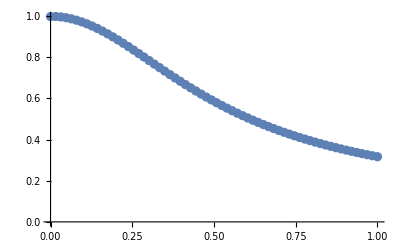

```mathematica
originB=Table[{(Roughness-1)/63,BRDFpartB[[Roughness]][[1]]},{Roughness,1,64}];
ListPlot[originB]
```

Function[x,1.0022-0.048193 x-3.51034 x^2+4.90069 x^3-2.03378 x^4]

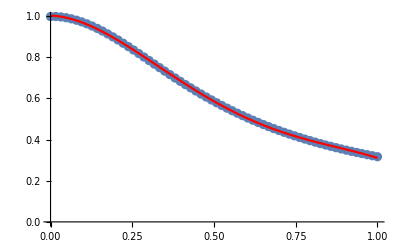

```mathematica
fittingMethod="Automatic";
(*fittingMethod="PrincipalAxis";*)
(*fittingMethod="LevenbergMarquardt";*)

modelOriginB=a+b*Sin[x]+c*Sin[x]^2+d*Sin[x]^3;
(*modelOriginB=Exp[-a*Sin[c*x]^b];*)
modelOriginB=a+b*x+c*x^2+d*x^3+e*x^4;
fittingOriginB = FindFit[originB,modelOriginB,{a,b,c,d,e},x,Method->fittingMethod];
modelOriginB =Function[x,Evaluate[ modelOriginB/.fittingOriginB]]
Show[
ListPlot[originB],
Plot[modelOriginB[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

#### Now, let’s attempt to fit all of our N.V curves, varying our roughness

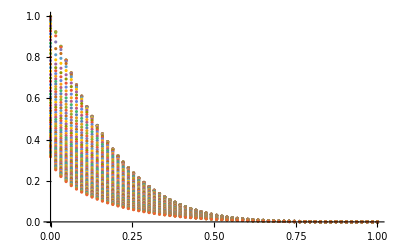

```mathematica
curvesB= Table[{(NdotV-1)/63, BRDFpartB[[Roughness]][[NdotV]]},{Roughness,1,64,1},{NdotV,1,64}];
ListPlot[curvesB,PlotRange->Full]
```

Let’s assume a 3rd degree polynomial can reasonnably represent all these curves...

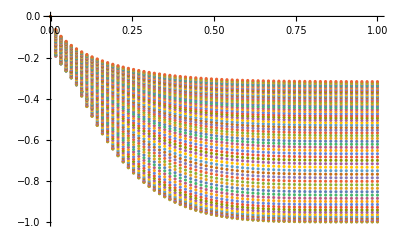

```mathematica
curvesBoffset=Table[{(NdotV-1)/63, BRDFpartB[[Roughness]][[NdotV]]-BRDFpartB[[Roughness]][[1]]},{Roughness,1,64,1},{NdotV,1,64}];
ListPlot[curvesBoffset,PlotRange->Full]
```

```mathematica
(* Find fitting for all our 64 roughness curves *)
(*modelCurveB=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5; becoming too instable!*)
(*modelCurveB=a+b*x+c*x^2+d*x^3;*)
modelCurveB=a*x+b*x^2+c*x^3+d*x^4+e*x^5;
fittingCurvesB = Table[FindFit[curvesBoffset[[curveIndex]],modelCurveB,{a,b,c,d,e},x,Method->fittingMethod],{curveIndex,1,64}];
Function[x,Evaluate[modelCurveB/.fittingCurvesB[[10]]]]
MatrixForm[fittingCurvesB]
```

Function[x,-4.88411 x+11.6386 x^2-16.3706 x^3+12.947 x^4-4.27954 x^5]

(a→-4.88273 | b→9.48336 | c→-9.07796 | d→4.23807 | e→-0.758186
a→-4.89208 | b→9.53364 | c→-9.19121 | d→4.3511 | e→-0.79948
a→-4.85846 | b→9.37124 | c→-8.84815 | d→4.02299 | e→-0.683184
a→-4.81979 | b→9.23333 | c→-8.62404 | d→3.85357 | e→-0.634852
a→-4.79176 | b→9.23702 | c→-8.8215 | d→4.16839 | e→-0.779146
a→-4.78037 | b→9.42105 | c→-9.53106 | d→5.05763 | e→-1.14856
a→-4.78714 | b→9.78768 | c→-10.7446 | d→6.50227 | e→-1.73294
a→-4.8094 | b→10.3063 | c→-12.3671 | d→8.38877 | e→-2.48566
a→-4.84399 | b→10.9432 | c→-14.298 | d→10.5994 | e→-3.35905
a→-4.88411 | b→11.6386 | c→-16.3706 | d→12.947 | e→-4.27954
a→-4.92428 | b→12.3437 | c→-18.4511 | d→15.283 | e→-5.18906
a→-4.96155 | b→13.0322 | c→-20.4686 | d→17.5303 | e→-6.05818
a→-4.99075 | b→13.6617 | c→-22.3121 | d→19.5702 | e→-6.84178
a→-5.01106 | b→14.2249 | c→-23.9651 | d→21.388 | e→-7.53541
a→-5.01953 | b→14.6985 | c→-25.3702 | d→22.9252 | e→-8.11768
a→-5.01683 | b→15.0876 | c→-26.5448 | d→24.2046 | e→-8.59865
a→-5.00216 | b→15.3859 | c→-27.4762 | d→25.2159 | e→-8.97544
a→-4.97685 | b→15.6037 | c→-28.1938 | d→25.9938 | e→-9.26225
a→-4.94333 | b→15.7588 | c→-28.7465 | d→26.5935 | e→-9.48088
a→-4.89991 | b→15.8384 | c→-29.1039 | d→26.9844 | e→-9.62039
a→-4.85008 | b→15.8682 | c→-29.3325 | d→27.2389 | e→-9.70862
a→-4.79344 | b→15.8448 | c→-29.426 | d→27.3519 | e→-9.74408
a→-4.73303 | b→15.7897 | c→-29.4388 | d→27.3812 | e→-9.74877
a→-4.66679 | b→15.6866 | c→-29.3285 | d→27.2814 | e→-9.70537
a→-4.59734 | b→15.5566 | c→-29.153 | d→27.117 | e→-9.63908
a→-4.52596 | b→15.4078 | c→-28.9318 | d→26.9079 | e→-9.55717
a→-4.45171 | b→15.2325 | c→-28.6445 | d→26.6317 | e→-9.45105
a→-4.3758 | b→15.0383 | c→-28.3083 | d→26.3057 | e→-9.32689
a→-4.2997 | b→14.8358 | c→-27.9515 | d→25.9604 | e→-9.19643
a→-4.22397 | b→14.6286 | c→-27.5818 | d→25.6034 | e→-9.06242
a→-4.14737 | b→14.4071 | c→-27.1746 | d→25.208 | e→-8.9145
a→-4.07198 | b→14.1868 | c→-26.7698 | d→24.8173 | e→-8.76925
a→-3.9982 | b→13.9702 | c→-26.3726 | d→24.4357 | e→-8.62804
a→-3.92507 | b→13.7499 | c→-25.964 | d→24.0428 | e→-8.48296
a→-3.85323 | b→13.5298 | c→-25.5519 | d→23.6457 | e→-8.33639
a→-3.783 | b→13.3128 | c→-25.1453 | d→23.2548 | e→-8.19262
a→-3.7142 | b→13.0973 | c→-24.7391 | d→22.8643 | e→-8.0492
a→-3.64699 | b→12.8854 | c→-24.3398 | d→22.4817 | e→-7.90914
a→-3.58167 | b→12.6792 | c→-23.9518 | d→22.1106 | e→-7.77355
a→-3.51851 | b→12.4802 | c→-23.5784 | d→21.7542 | e→-7.64346
a→-3.45743 | b→12.2879 | c→-23.218 | d→21.4108 | e→-7.51822
a→-3.39857 | b→12.1035 | c→-22.8738 | d→21.0833 | e→-7.39896
a→-3.34098 | b→11.9209 | c→-22.5319 | d→20.7586 | e→-7.28103
a→-3.28514 | b→11.7435 | c→-22.1999 | d→20.444 | e→-7.16704
a→-3.23166 | b→11.5766 | c→-21.8927 | d→20.1559 | e→-7.06332
a→-3.17947 | b→11.4115 | c→-21.5855 | d→19.8663 | e→-6.95872
a→-3.12929 | b→11.2535 | c→-21.2926 | d→19.5903 | e→-6.85906
a→-3.08064 | b→11.1008 | c→-21.0112 | d→19.3269 | e→-6.76439
a→-3.03403 | b→10.9568 | c→-20.7497 | d→19.0843 | e→-6.67768
a→-2.98906 | b→10.8184 | c→-20.499 | d→18.8521 | e→-6.5948
a→-2.9458 | b→10.6853 | c→-20.2575 | d→18.6279 | e→-6.51456
a→-2.90351 | b→10.5528 | c→-20.0138 | d→18.4 | e→-6.43278
a→-2.86318 | b→10.4279 | c→-19.7849 | d→18.1859 | e→-6.35576
a→-2.82411 | b→10.307 | c→-19.564 | d→17.9798 | e→-6.28179
a→-2.78655 | b→10.1921 | c→-19.3565 | d→17.7878 | e→-6.21326
a→-2.75034 | b→10.0822 | c→-19.1594 | d→17.6063 | e→-6.14862
a→-2.71532 | b→9.9766 | c→-18.9715 | d→17.4342 | e→-6.08762
a→-2.68159 | b→9.87604 | c→-18.7948 | d→17.2739 | e→-6.03118
a→-2.64911 | b→9.7799 | c→-18.6268 | d→17.1221 | e→-5.97777
a→-2.61789 | b→9.68804 | c→-18.4666 | d→16.9771 | e→-5.9267
a→-2.58756 | b→9.59797 | c→-18.3081 | d→16.8329 | e→-5.87569
a→-2.55816 | b→9.50982 | c→-18.1515 | d→16.6894 | e→-5.82478
a→-2.52975 | b→9.42501 | c→-18.0014 | d→16.5522 | e→-5.77615
a→-2.50279 | b→9.34686 | c→-17.866 | d→16.4298 | e→-5.733)

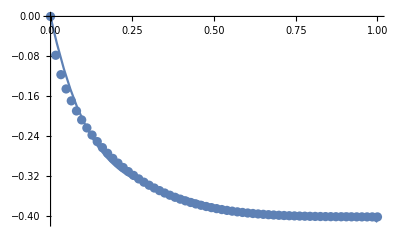

```mathematica
Show[Plot[modelCurveB/.fittingCurvesB[[50]],{x,0,1},PlotRange->Full],
ListPlot[curvesBoffset[[50]],PlotRange->Full]]
```

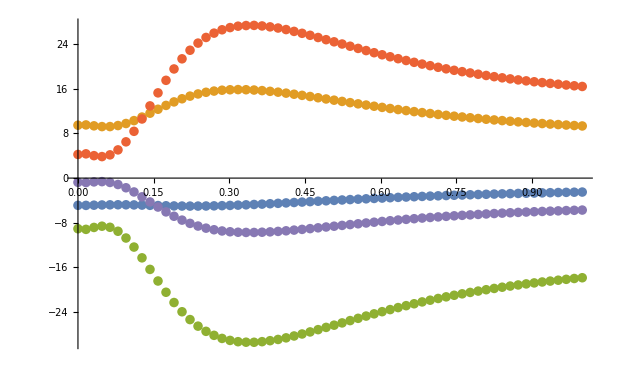

```mathematica
curvesBa = Table[{(i-1)/63, a/.fittingCurvesB[[i]]},{i,1,64}];
curvesBb = Table[{(i-1)/63, b/.fittingCurvesB[[i]]},{i,1,64}];curvesBc = Table[{(i-1)/63, c/.fittingCurvesB[[i]]},{i,1,64}];curvesBd = Table[{(i-1)/63, d/.fittingCurvesB[[i]]},{i,1,64}];
curvesBe = Table[{(i-1)/63, e/.fittingCurvesB[[i]]},{i,1,64}];(*curvesBf = Table[{(i-1)/63, f/.fittingCurvesB[[i]]},{i,1,64}];ListPlot[{curvesBa,curvesBb,curvesBc,curvesBd,curvesBe,curvesBf}]*)
ListPlot[{curvesBa,curvesBb,curvesBc,curvesBd,curvesBe}]
```

#### Now fitting a,b,c,d,e

Now that we know the behavior of coefficients a, b, c, d & e depending on roughness, we can try and fit them too!

```mathematica
fittingMethod="Automatic";
(*fittingMethod="PrincipalAxis";*)
(*fittingMethod="InteriorPoint";*)
(*fittingMethod="Newton";*)
(*fittingMethod="QuasiNewton";*)
(*fittingMethod="LevenbergMarquardt";*)
(*fittingMethod="ConjugateGradient";*)

generalModelCoeffs = a+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
(*generalModelCoeffs = a+b*x+c*Exp[d*x]*Cos[e*x];*)

(* Use modelOriginB function for our initial parameter a *)
(*generalModelCoeffs = Evaluate[modelOriginB[x]]+b*x+c*x^2+d*x^3+e*x^4+f*x^5*)
```

Function[x,-4.82878+0.740486 x-20.403 x^2+87.9274 x^3-110.582 x^4+44.7199 x^5]

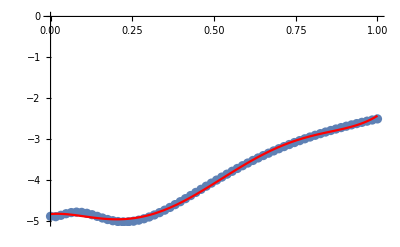

```mathematica
modelCoeffA=generalModelCoeffs;
fittingCoeffA = FindFit[curvesBa,modelCoeffA,{{a,-5},{b,2},{c,0.1},{d,-1},e,f},x,Method->fittingMethod];
modelCoeffA = Function[x,Evaluate[modelCoeffA/.fittingCoeffA]]
Show[
ListPlot[curvesBa],
Plot[modelCoeffA[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

Function[x,8.90305+0.549578 x+247.296 x^2-848.162 x^3+982.996 x^4-382.856 x^5]

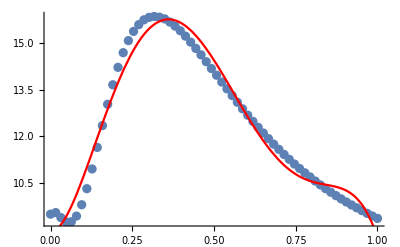

```mathematica
modelCoeffB=generalModelCoeffs;
fittingCoeffB = FindFit[curvesBb,modelCoeffB,{{a,11},{b,0},{c,10},{d,-0.1},{e,4},f},x,Method->fittingMethod];
modelCoeffB = Function[x,Evaluate[modelCoeffB/.fittingCoeffB]]
Show[
ListPlot[curvesBb],
Plot[modelCoeffB[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

Function[x,-7.25157-16.3814 x-632.735 x^2+2194.23 x^3-2548.98 x^4+994.905 x^5]

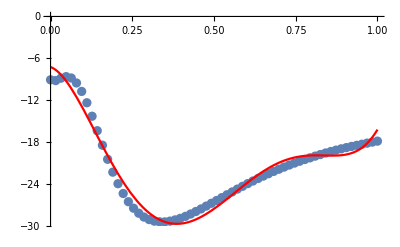

```mathematica
modelCoeffC=generalModelCoeffs;
fittingCoeffC = FindFit[curvesBc,modelCoeffC,{{a,-18},{b,0},{c,10},{d,-1.0},{e,2},f},x,Method->fittingMethod];
modelCoeffC = Function[x,Evaluate[modelCoeffC/.fittingCoeffC]]
Show[
ListPlot[curvesBc],
Plot[modelCoeffC[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

Function[x,2.03283+29.5558 x+639.567 x^2-2286. x^3+2682.68 x^4-1053.21 x^5]

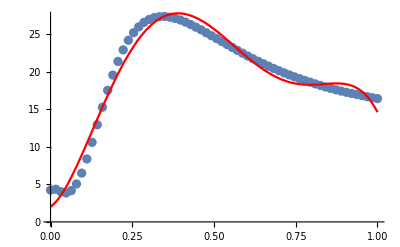

```mathematica
modelCoeffD=generalModelCoeffs;
fittingCoeffD = FindFit[curvesBd,modelCoeffD,{{a,18},{b,0},{c,-10},{d,-1},{e,3},f},x,Method->fittingMethod];
modelCoeffD = Function[x,Evaluate[modelCoeffD/.fittingCoeffD]]
Show[
ListPlot[curvesBd],
Plot[modelCoeffD[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

Function[x,0.151268-14.6935 x-228.942 x^2+844.287 x^3-1001.12 x^4+395.284 x^5]

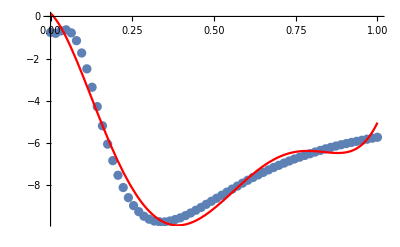

```mathematica
modelCoeffE=generalModelCoeffs;
fittingCoeffE = FindFit[curvesBe,modelCoeffE,{{a,-5},{b,-0.5},{c,5},{d,-1},{e,3},f},x,Method->fittingMethod];
modelCoeffE = Function[x,Evaluate[modelCoeffE/.fittingCoeffE]]
Show[
ListPlot[curvesBe],
Plot[modelCoeffE[x],{x,0,1},PlotRange->Full,PlotStyle->Red]
]
```

### Plotting the result & comparing with data

```mathematica
(*fitB[NdotV_,r_]:=modelCoeffA[r]+modelCoeffB[r]*NdotV+modelCoeffC[r]*NdotV^2+modelCoeffD[r]*NdotV^3;*)
(*fitB[NdotV_,r_]:=modelCoeffA[r]+modelCoeffB[r]*NdotV+modelCoeffC[r]*NdotV^2+modelCoeffD[r]*NdotV^3+modelCoeffE[r]*NdotV^4;*)

fitB[NdotV_,r_]:=modelOriginB[r]+modelCoeffA[r]*NdotV+modelCoeffB[r]*NdotV^2+modelCoeffC[r]*NdotV^3+modelCoeffD[r]*NdotV^4+modelCoeffE[r]*NdotV^5;

Show[Plot3D[fitB[(NdotV-1)/63,(r-1)/63],{NdotV,1,64},{r,1,64},PlotRange->Full,AxesLabel->{"N.V","Roughness"},PlotStyle->ColorData["RedBlueTones"]],
ListPlot3D[BRDFpartB,PlotRange->Full,AxesLabel->{"N.V","Roughness"}]]
```

-Graphics3D-

#### Test directly fitting a 3D function...

```mathematica
data=Table[{(Mod[i,64])/63,Floor[i/64] / 63,BRDFpartB[[1+Floor[i/64]]][[1+Floor[Mod[i,64]]]]},{i,0,128,1}];
```

```mathematica
Clear[a,b,c,d,f,g]
pipoModel =c*Exp[a*(x-x0)+b*(y-y0)];
(*pipoModel =a+b*x+c*x^2 d*x^3+e*y+f*y^2+ g*x*y;*)
data=Table[{Mod[i,64]/63,Floor[i/64] / 63,BRDFpartB[[1+Floor[i/64]]][[1+Floor[Mod[i,64]]]]},{i,0,64*64-1,1}];
ListPlot3D[data,PlotRange->Full,AxesLabel->{"x","y"}]
pipoFit=FindFit[data,pipoModel,{{a,0},{b,1},{c,1},d,e,{f,1},g,h,i,x0,y0,x1,y1},{x,y},Method->"Automatic"]
pipoModel=Function[{x,y},Evaluate[pipoModel/.pipoFit]];
Plot3D[pipoModel[x,y],{x,0,1},{y,0,1},PlotRange->Full,AxesLabel->{"x","y"}]
```

-Graphics3D-

{a→-5.6487,b→-1.44273,c→0.527851,d→1.,e→1.,f→1.,g→1.,h→1.,i→1.,x0→-0.308139,y0→1.72007,x1→1.,y1→1.}

-Graphics3D-

```mathematica
Show[ListPlot3D[data,PlotRange->Full],Plot3D[pipoModel[x,y],{x,0,1},{y,0,1},PlotRange->Full,PlotStyle->Hue[0.58,0.5,0.67]]]
```

-Graphics3D-

### Examining the Beckmann distribution

```mathematica
beckman[a_,m_]:= Exp[-(Tan[a]/m)^2] / (4*Pi*m^2);
Manipulate[ { Plot[beckman[a,m], {a,0.0,π/2},PlotRange->Full], beckman[0,m]},{{m,0.2},1/100,π/2}]
```

```mathematica
Integrate[beckman[a,0.1],{a,0,∞}]
```

∫_0^∞ 7.95775 ⅇ^(-100. Tan[a]^2)ⅆa

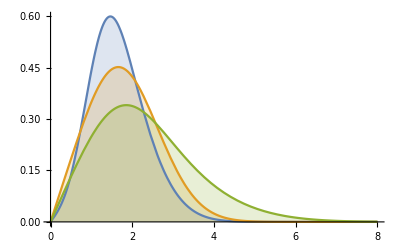

```mathematica
Plot[Evaluate@Table[PDF[BeckmannDistribution[1,-1,1,σ2],x],{σ2,{1/2,1,2}}],{x,0,8},Filling->Axis]
```

## Visualizing shadowing term G_Schlick(L,V,H)

Assuming L⃗ is the reflection of V⃗ by the plane of normal N⃗ we can write L⃗ = -V⃗+ 2(N⃗.V⃗).N⃗
G_Schlick(v) = (n.v)/((n.v)(1-k) + k) where k=(m+1)^2/8 and m the materials roughness.

```mathematica
Gschlick[x_,k_]:= x/(x*(1-k)+k)
```

```mathematica
Manipulate[Plot[Gschlick[Cos[x],(m+1)^2/8]^2,{x,0,π/2}], {{m,0.01},0,1}]
```

## Paraboloïd Shadow Mapping

```mathematica
Plot3D[{1-x^2-y^2,0},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

### Using a sigmoïd to simulate the step function

```mathematica
sigmoid[x_,k_] := 1 / (1+Exp[-k*x]);
Manipulate[Plot[sigmoid[x,k], {x,-10, 10},PlotRange->Full], {{k,1},1/100,100}]
```

```mathematica
Series[sigmoid[x,10],{x,0,8}]
```

1/2+(5 x)/2-(125 x^3)/6+(625 x^5)/3-(265625 x^7)/126+O[x]^9

```mathematica
approx[x_]:=1/2+(5 x)/2-(125 x^3)/6+(625 x^5)/3-(265625 x^7)/126
```

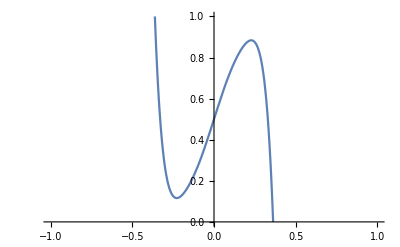

```mathematica
Plot[approx[x],{x,-1,1},PlotRange->{0,1}]
```

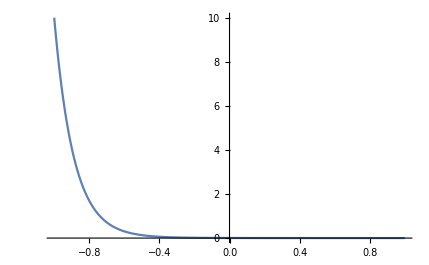

```mathematica
a = 1.0;
b =  0.1;
altitude = 100.0;
hitDistance = 100.0;
density[dy_]:= a  Exp[-b * altitude] (1 - Exp[-b * dy * hitDistance]) / (b * dy);
Plot[density[x], {x, -1.0, 1 }, PlotRange->Full]
```